```mathematica
ClearAll["Global`*"]
```

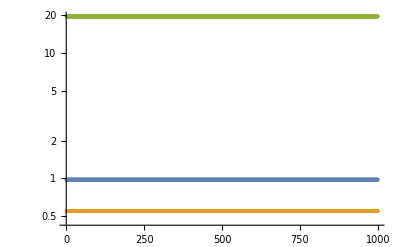

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
InvaderGrowth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderGrowth,InvaderStarvation,InvaderRecovery}
);
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,λ2_,σ2_,ρ2_,β2_,T_,F0_,H0_,FI0_,HI0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],

FI'[t] ==λ2*FI[t]-σ2*(1-R[t])*FI[t] +ρ2* R[t] * HI[t],
HI'[t] ==σ2*(1-R[t])*FI[t] - ρ2* R[t]*HI[t] - μ*HI[t],

R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t] +ρ2*H2[t] + β2*F2[t] )*R[t] ,

F[0]==F0,H[0]==H0,FI[0]==FI0,HI[0]==HI0,R[0]==R0},{F,H,R,FI,HI},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderGrowth = RF[[7]];
InvaderStarvation = RF[[8]];
InvaderRecovery=RF[[9]];
With[{
α=Resourcegrowth,λ=Growth,σ=Starvation,ρ=Recovery,β=Maintenance,
λ2=InvaderGrowth,σ2=InvaderStarvation,ρ2=InvaderRecovery,β2=InvaderMaintenance,
μ=mortality,T=100000000,PropInvade=0.10},
F0=(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*(1-PropInvade);
R0= (μ (-λ+σ))/(λ ρ+μ σ);
F0=0;
H0=(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))*PropInvade;
R0= (μ (-λ+σ))/(λ ρ+μ σ);
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[1;;1000,1]];
Htraj = Flatten[Traj,1][[1;;1000,2]];
Rtraj = Flatten[Traj,1][[1;;1000,3]];
ListLogPlot[{Rtraj,Htraj,Ftraj},PlotRange->All]
]
```

```mathematica
Traj
```

{{{10000.,10000.,10000.}},{{100.737,13154.8,-2.60066×10^-10}},997,{{-1.54663×10^75,1.54663×10^75,-3.21325×10^83}},{{-1.5544×10^75,1.5544×10^75,-3.22938×10^83}}}
 |  |  |  |